## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["AnalyticalSolarDevices`","C:\\Users\\Liu Haohui\\OneDrive - envision\\Development\\Analytical models development\\analytical-solar-cell-and-module\\AnalyticalSolarDevices.wl"];
T=298.15;
spec=<<spectrum_AM15G;
```

## Calculate cell output under a particular spectrum and temperature

Single junction cells

```mathematica
SiCell[spec,T]
```

{{{0.736677,-509.621},{0.714354,-325.979},{0.69203,-154.738},{0.669707,-0.000235349},{0.647383,132.919},{0.62506,238.269},{0.602736,312.444},{0.602736,312.444},{0.585993,348.607},{0.569251,371.44},{0.560879,379.1},{0.556694,382.202},{0.552508,384.891},{0.548322,387.217},{0.544137,389.223},{0.535765,392.436},{0.50228,398.738},{0.468795,400.526},{0.401824,401.206},{0.267883,401.389},{0.133941,401.523},{0.,401.657},{-0.133941,401.791},{-0.267883,401.925},{-0.401824,402.059},{-0.535765,402.193},{-0.669707,402.327},{-0.803648,402.461},{-0.93759,402.594}},401.693,0.669707,0.790916,212.769,382.202,0.556694}

```mathematica
SiCell[400,T,DeviceQE->{}]
```

{{{0.736558,-509.013},{0.714238,-325.532},{0.691918,-154.489},{0.669598,-0.000236845},{0.647278,132.61},{0.624958,237.598},{0.602638,311.408},{0.585898,347.34},{0.569158,370.002},{0.560788,377.599},{0.556603,380.676},{0.552418,383.342},{0.548233,385.647},{0.544048,387.636},{0.535678,390.821},{0.502198,397.067},{0.468719,398.839},{0.401759,399.513},{0.267839,399.696},{0.13392,399.83},{0.,399.964},{-0.13392,400.098},{-0.267839,400.232},{-0.401759,400.366},{-0.535678,400.5},{-0.669598,400.634},{-0.803518,400.767},{-0.937437,400.901}},400.,0.669598,0.791092,211.885,380.676,0.556603}

```mathematica
SiCell[spec,T,{"V",0.3}]
```

{126.845,422.818,0.3}

```mathematica
SiCell[spec,T,CellParameters->parameters["PERC"],CellQE->EQE["PERC"]]
```

{{{0.669707,-1.66294×10^-10},{0.647383,132.92},{0.62506,238.269},{0.602736,312.444},{0.585993,348.607},{0.569251,371.44},{0.560879,379.1},{0.556694,382.202},{0.552508,384.891},{0.548322,387.217},{0.544137,389.223},{0.535765,392.436},{0.50228,398.738},{0.468795,400.526},{0.401824,401.206},{0.267883,401.389},{0.133941,401.523},{0.,401.657},{-0.133941,401.791},{-0.267883,401.925},{-0.401824,402.059},{-0.535765,402.193},{-0.669707,402.327},{-0.803648,402.461},{-0.937589,402.594}},401.693,0.669707,0.790916,212.769,382.202,0.556694}

```mathematica
GaAsCell[spec,T]
```

{{{1.22126,-769.805},{1.18425,-482.547},{1.14724,-220.987},{1.11024,-9.57486×10^-9},{1.07323,159.568},{1.05472,211.506},{1.03622,246.17},{1.02697,258.173},{0.999212,279.56},{0.992273,282.576},{0.985334,284.987},{0.978395,286.913},{0.971456,288.452},{0.957578,290.669},{0.9437,292.1},{0.888188,294.377},{0.666141,295.297},{0.444094,295.526},{0.222047,295.748},{0.,295.97},{-0.222047,296.192},{-0.444094,296.414},{-0.666141,296.637},{-0.888188,296.859}},296.,1.11024,0.854481,280.808,284.987,0.985334}

tandem cell IV curve

```mathematica
output=TwoTer$GaAsSi[spec,T,CouplingEfficiency->0.5]
```

{{{-0.0679982,187.942},{0.136087,187.755},{0.339862,187.567},{0.543281,187.38},{0.746478,187.192},{0.943454,187.005},{1.55437,184.668},{1.59608,182.33},{1.61988,179.993},{1.63672,177.655},{1.66049,172.98},{1.67742,168.305},{1.70151,158.955},{1.71886,149.604},{1.74392,130.904},{1.76236,112.203},{1.78981,74.8022},{1.81082,37.4011},{1.82836,0.}},187.942,1.82836,0.848501,291.567,179.993,1.61988,190.125,187.005}

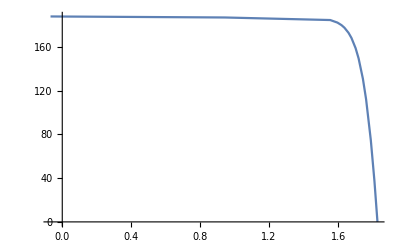

```mathematica
ListLinePlot[output[[1]],PlotRange->Full]
```

```mathematica
output=TwoTer$InGaPSi[spec,T,CouplingEfficiency->0.5]
```

{{{-0.0362837,146.673},{0.110453,146.527},{0.257044,146.38},{0.403488,146.234},{0.549785,146.088},{0.694475,145.942},{1.91938,144.118},{1.98746,142.294},{2.0147,140.469},{2.03168,138.645},{2.0536,134.996},{2.06823,131.348},{2.08813,124.051},{2.10204,116.754},{2.12175,102.159},{2.13603,87.5653},{2.15684,58.3768},{2.17226,29.1884},{2.18466,0.}},146.673,2.18466,0.883195,283.004,140.469,2.0147,145.942,217.511}

```mathematica
TwoTer$InGapGaAsSi[spec,T,CouplingEfficiency->{0.5,0.5}]//AbsoluteTiming
```

{0.0751321,{{{-0.346433,117.874},{0.899354,116.707},{2.12383,115.551},{2.88822,114.107},{2.94336,112.662},{2.97265,111.218},{2.99369,109.774},{3.02438,106.885},{3.04707,103.996},{3.08037,98.2186},{3.10486,92.441},{3.14047,80.8859},{3.16649,69.3308},{3.20436,46.2205},{3.23229,23.1103},{3.25476,0.}},117.874,3.25476,0.864343,331.606,112.662,2.94336,122.42,115.551,123.694}}

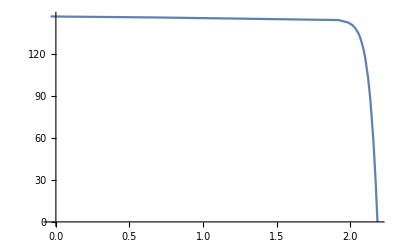

```mathematica
ListLinePlot[output[[1]],PlotRange->Full]
```

GaAs cell with various shunts.

```mathematica
Rsh={100,500,1000,5000,10000}*10^-4;
```

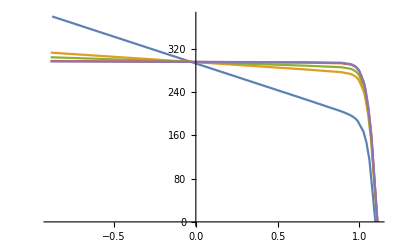

```mathematica
outputs=GaAsCell[spec,T,CellParameters-><|"J01"->6*^-17,"J02"->1*^-8,"Rs"->1*^-4,"Rsh"->#|>]&/@Rsh;
ListLinePlot[outputs[[All,1]],PlotRange->Full]
```

## Investigate the effect of temperature

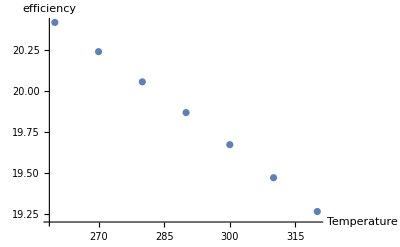

```mathematica
Temp=Range[260,320,10];
eff=Table[InGaPCell[spec,t][[5]]/10,{t,Temp}];
ListPlot[{Temp,eff}//Transpose,AxesLabel->{"Temperature","efficiency"}]
```

## Investigate effect of coupling efficiency

{29.1142,29.1252,29.1359,29.1463,29.1566,29.1667,29.1766,29.1864}

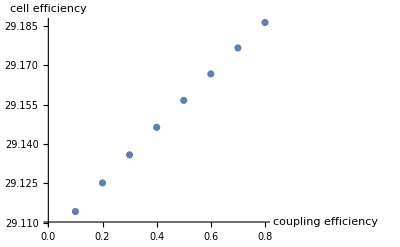

```mathematica
couplingEff=Range[0.1,0.8,0.1];
eff=Table[TwoTer$GaAsSi[spec,T,CouplingEfficiency->eta][[5]]/10,{eta,couplingEff}]
ListPlot[{couplingEff,eff}//Transpose,AxesLabel->{"coupling efficiency","cell efficiency"}]
```